```mathematica
(* Guy Mongelli                                 ChE 400
Prof. Clark                                   11/18/2010   *)
```

```mathematica
(*Assignment #9  *)
```

```mathematica
(*Challenge Problem *)
```

```mathematica
(*Part B *)
```

```mathematica
b=10
```

10

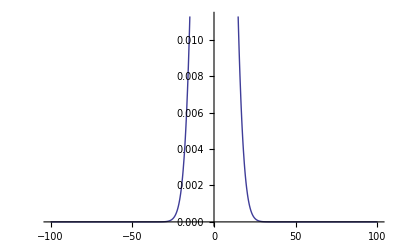

```mathematica
Plot[1/b*Exp[-x^2/b^2],{x,-100,100}]
```

```mathematica
d=100000
```

100000

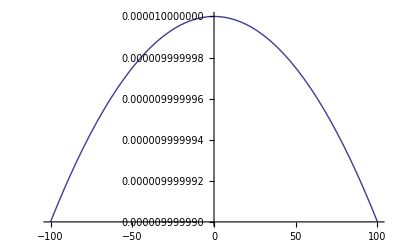

```mathematica
Plot[1/d*Exp[-x^2/d^2],{x,-100,100}]
```

```mathematica
Plot[DiracDelta,{x,-1,1}]
```

-Graphics-

```mathematica
d=1
```

1

```mathematica
Element[{b,t},Reals]
```

(b|t)∈Reals

```mathematica
∫_(-∞)^∞ p*c*e/p/c*Exp[-k^2*b^2/4]ⅆk
```

e If[Re[b^2]>0,(2 √π)/(√(b^2)),Integrate[ⅇ^(-1/4 b^2 k^2),{k,-∞,∞},Assumptions→Re[b^2]≤0]]

```mathematica
(*Part D *)
```

```mathematica
e=1;b=1;
p=1;c=1;d=1
```

1

```mathematica
T[k_,t_]=e/p/c*Exp[-k^2*b^2/4]*Exp[-k^2*d*t]
```

ⅇ^(-k^2/4-k^2 t)

```mathematica
P[y_]:=∫_(-∞)^∞ p*c*T[k,t]ⅆk
```

```mathematica
P[1]
```

If[Re[D t]>-1/4,(2 ⅇ √π)/(√(1+4 D t)),Integrate[ⅇ^(1-1/4 k^2 (1+4 D t)),{k,-∞,∞},Assumptions→Re[D t]≤-1/4]]

```mathematica
Plot[P[y],{y,-10,10}]
```

NIntegrate::inumr: The integrand ⅇ^1 - 1/4 k^2 (1 + 4 D t) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

-Graphics-